{{1.,2.},{1.,5.},{4.,7.5},{9.,7.},{8.3,4.},{6.,0.},{1.,2.}}

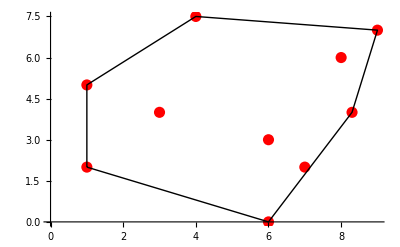

```mathematica
points= ReadList["/Users/valeriy/Documents/3course/compsci/Валединский/Convex_Hull-master/points.txt", Real];
hulll = ReadList["/Users/valeriy/Documents/3course/compsci/Валединский/Convex_Hull-master/output.txt", Real];
partpoints=Partition[points, 2];
parthull = Partition[hulll, 2];
parthull = Insert[ parthull ,parthull[[1]],-1]
Show[{
ListPlot[partpoints, PlotStyle->{ PointSize[0.02],Red} ],
Graphics[Line[parthull]]

}]
```